```mathematica
numfiles = 28;
numsims = 1;
va =1.2
ara=1.6;
pot = 10;
ba = (va/ara)^(1/3);
ella = ara*ba;
ellb = ba;
ellc = ba;
R=1/2;
(*R=1.2/2;*)
numparticles = 4;
percentvolume = 0.9;
scaling = Table[(1)^(1/3),{i,numfiles/3}];
scaling=Catenate[{ scaling,Table[(2)^(1/3),{i,numfiles/3}]}];
scaling=Catenate[ {scaling,Table[(4)^(1/3),{i,numfiles/3}]}];
sella = ella;
sellb = ellb;
sellc = ellc;
```

2.48

```mathematica
(*filename = "test10_pot3_multisim";*)
ar = "AR"<>ToString[ara];
v = "_V"<>ToString[va];
filenamea = "Graduate_Research2/Example code/C_elegans_test/"<>ar<>v<>"_r0.7_N4_div10_n5e-5_Tdiv_pot"<>ToString[pot];
(*filenameb=ar<>v<>"_r0.7_N4_div10_n5e-5_rand";*)
divconst = 3*10;
filename = filenamea(*<>filenameb*)
savefile = "plots_R1.2";
simnum = 1;
```

2018 Simulator Framework/Testing heat/test4_nopot_sims/AR1_V2.48_r0.7_N4_div10_n5e-5_order_pot10

```mathematica
"a"<>"b"
```

ab

```mathematica
gnudata1=Table[Import["/Users/Valhalla/Documents/UCSB/Campas_Research/Graduate_Research/New_Simulator/Sims with voro/"<>filename<>"/dodec_sim"<>ToString[i-1]<>"_"<>ToString[j-1]<>".dat"],{i,numsims},{j,numfiles}];
```

```mathematica
adjdata=Table[Import["/Users/Valhalla/Documents/UCSB/Campas_Research/Graduate_Research/New_Simulator/Sims with voro/"<>filename<>"/adj_"<>ToString[i-1]<>".csv"],{i,numsims}];
```

```mathematica
areadata=Table[Import["/Users/Valhalla/Documents/UCSB/Campas_Research/Graduate_Research/New_Simulator/Sims with voro/"<>filename<>"/area_"<>ToString[i-1]<>".csv"],{i,numsims}];
```

```mathematica
posdata=Table[Import["/Users/Valhalla/Documents/UCSB/Campas_Research/Graduate_Research/New_Simulator/Sims with voro/"<>filename<>"/pos_"<>ToString[i-1]<>".csv"],{i,numsims}];
```

```mathematica
distdata=Table[Import["/Users/Valhalla/Documents/UCSB/Campas_Research/Graduate_Research/New_Simulator/Sims with voro/"<>filename<>"/dist_"<>ToString[i-1]<>".csv"],{i,numsims}];
```

```mathematica
Dimensions[adjdata[[1]]]
```

{128,4}

```mathematica
point1 = posdata[[All,All,{2,3,4}]];
point2 = posdata[[All,All,{5,6,7}]];
point3 = posdata[[All,All,{8,9,10}]];
point4 = posdata[[All,All,{11,12,13}]];
(*point5 = posdata[[All,All,{14,15,16}]];
point6 = posdata[[All,All,{17,18,19}]];
point7 = posdata[[All,All,{20,21,22}]];
point8 = posdata[[All,All,{23,24,25}]];*)
```

```mathematica
adjsize = Dimensions[adjdata][[3]];
divtime = Dimensions[adjdata][[2]]/adjsize;
```

```mathematica
adjmat = Table[adjdata[[j,i;;i+(adjsize-1),All]],{j,numsims},{i,1,Dimensions[adjdata][[2]],adjsize}];
```

```mathematica
areamat = Table[areadata[[j,i;;i+(adjsize-1),All]],{j,numsims},{i,1,Dimensions[areadata][[2]],adjsize}];
```

```mathematica
Dimensions[adjmat]
```

{1,32,4,4}

```mathematica
adjsize
```

4

```mathematica
(*Dimensions[adjdata[[100]]]*)
```

```mathematica
(*Manipulate[areamat[[simnum,i]]//MatrixForm,{i,1,Dimensions[areamat][[2]],1}]*)
```

```mathematica
(*Manipulate[MatrixPlot[adjmat[[simnum,i]]],{i,1,Dimensions[adjmat][[2]],1}]*)
```

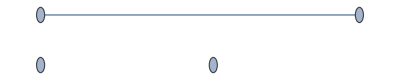
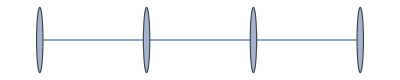
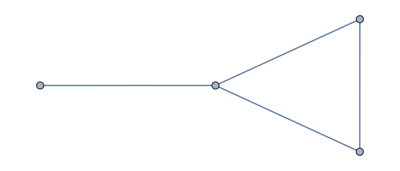
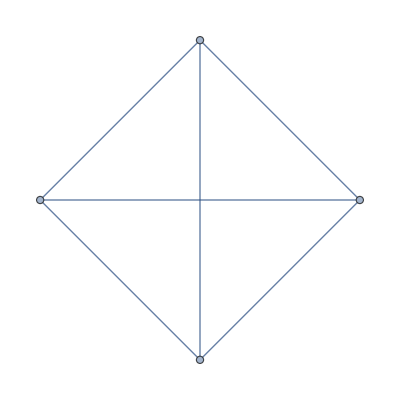
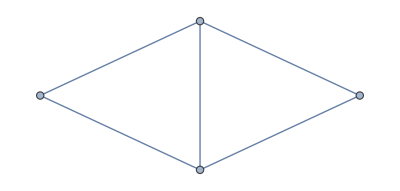
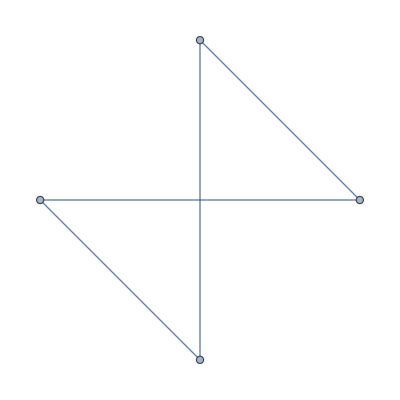
```mathematica
adjgraphs = Table[AdjacencyGraph[adjmat[[j,i]]],{j,numsims},{i,divtime}];
mat1 ={{0,1,1,1},{1,0,1,1},{1,1,0,1},{1,1,1,0}};
graph1=AdjacencyGraph[mat1];
standardgraphs ={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
Do[
Do[counter = 0;
Do[If[IsomorphicGraphQ[adjgraphs[[k,l]],standardgraphs[[j]]],counter =counter+1;,],{j,Length[standardgraphs]}]
If[counter==0,AppendTo[standardgraphs,adjgraphs[[k,l]]],],{l,divtime}],{k,numsims}]
```

```mathematica
standardgraphs;
```

```mathematica
graphdata =Table[{},{i,divtime}];
graphcounter = Dimensions[standardgraphs][[1]];
Do[Do[Do[If[IsomorphicGraphQ[adjgraphs[[j,i]],standardgraphs[[k]]],AppendTo[graphdata[[i]],k],],{k,1,graphcounter}],{i,divtime}],{j,numsims}]
```

```mathematica
Dimensions[graphdata]
```

{32,1}

```mathematica
(*graphdata[[100]]*)
```

```mathematica
counts =Table[{(i/divtime)*divconst,j,Count[graphdata[[i]],j]/numsims},{i,divtime},{j,graphcounter}];
```

```mathematica
(*counts[[21]]*)
```

```mathematica
positions = Position[counts[[All,All,3]],0];
```

```mathematica
counttest = Delete[counts,positions];
```

```mathematica
Dimensions[counttest]
```

{32,1,3}

```mathematica
countpoints = counttest[[All,All,{1,3}]];
```

```mathematica
colortable = Flatten[Table[Hue[counttest[[i,j,2]]/graphcounter],{i,divtime},{j,Dimensions[counttest[[i]]][[1]]}]];
```

```mathematica
flatcountpoints = Flatten[countpoints,1];
```

```mathematica
flatcountpointsa = Table[{flatcountpoints[[i]]},{i,Dimensions[flatcountpoints][[1]]}];
```

```mathematica
Dimensions[gnudata1]
```

{1,28}

```mathematica
numlines1 = Table[Length[Position[gnudata1[[j,i]],{}]]/2,{j,numsims},{i,numfiles}];
```

```mathematica
Dimensions[numlines1]
```

{1,28}

```mathematica
(*numlines1[[3]]*)
```

```mathematica
lines1 = Table[{},{k,numsims},{i,numfiles},{j,numlines1[[k,i]]}];
Do[Do[counter1 = 1;
Do[If[gnudata1[[k,j,i]]≠{},AppendTo[lines1[[k,j,counter1]],gnudata1[[k,j,i]]],counter1= counter1 + 0.5],{i,Dimensions[gnudata1[[k,j]]][[1]]}],{j,numfiles}],{k,numsims}]
```

```mathematica
adjnumcell=1;
```

```mathematica
Table[FirstPosition[graphdata[[((numfiles)/3)*2+2]],i],{i,3,Length[standardgraphs],1}]
Table[FirstPosition[graphdata[[-1]],i],{i,3,Length[standardgraphs],1}]
```

Part::pkspec1: The expression 62/3 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{Missing[NotFound],Missing[NotFound],Missing[NotFound],{1,23,1},Missing[NotFound],{1,22,1}}

{Missing[NotFound],Missing[NotFound],Missing[NotFound],{1},Missing[NotFound],Missing[NotFound]}

```mathematica
simnum =1;
(*Manipulate[Grid[{{Graphics3D[{Line[lines1[[x]]]},Boxed->False]},{areamat[[x]]//MatrixForm},{adjgraphs[[x]]}}],{x,1,numfiles,1}]*)
Manipulate[Show[{ListPointPlot3D[{{point1[[simnum,x,1]],point1[[simnum,x,2]],point1[[simnum,x,3]]},{point2[[simnum,x,1]],point2[[simnum,x,2]],point2[[simnum,x,3]]},{point3[[simnum,x,1]],point3[[simnum,x,2]],point3[[simnum,x,3]]},{point4[[simnum,x,1]],point4[[simnum,x,2]],point4[[simnum,x,3]]}},
PlotRange->{{-2.5,2.5},{-2.5,2.5},{-2.5,2.5}},PlotStyle->PointSize[0.1],BoxRatios->{1,1,1},Boxed->False,Axes->False],Graphics3D[{Opacity[0],Ellipsoid[{0,0,0},{sella,sellb,sellc}]}],Graphics3D[{Line[lines1[[simnum,x]]]},Boxed->False]},ViewPoint->Top],{x,1,numfiles,1}]
```

```mathematica
Show[{Graphics3D[Sphere[{0,0,0},1]],Graphics3D[Sphere[{1,0,0},(1/0.9)^(1/3)]]}]
```

-Graphics3D-

```mathematica
Show[Graphics3D[{Line[lines1[[simnum,-1]]]},Boxed->False](*,Graphics3D[{Line[lines1[[simnum,3]]]},Boxed->False]}*)]
```

-Graphics3D-

```mathematica
flatcountpointsa
```

{{{15/16,1}},{{15/8,1}},{{45/16,1}},{{15/4,1}},{{75/16,1}},{{45/8,1}},{{105/16,1}},{{15/2,1}},{{135/16,1}},{{75/8,1}},{{165/16,1}},{{45/4,1}},{{195/16,1}},{{105/8,1}},{{225/16,1}},{{15,1}},{{255/16,1}},{{135/8,1}},{{285/16,1}},{{75/4,1}},{{315/16,1}},{{165/8,1}},{{345/16,1}},{{45/2,1}},{{375/16,1}},{{195/8,1}},{{405/16,1}},{{105/4,1}},{{435/16,1}},{{225/8,1}},{{465/16,1}},{{30,1}}}

```mathematica
plot =ListPlot[flatcountpointsa,PlotStyle->colortable,PlotRange->{All,{0,1.1}},Frame->True];
legend = Table[{Hue[i/graphcounter],standardgraphs[[i]]},{i,graphcounter}];
```

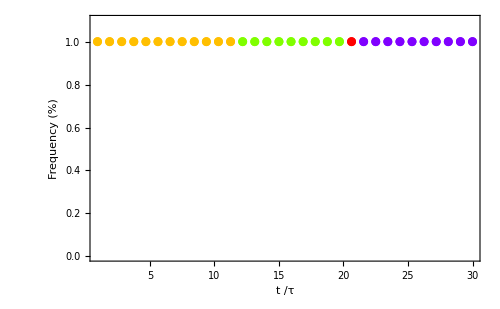

```mathematica
niceplot =Show[{plot},Axes->{False,False},FrameLabel->{"t /τ","Frequency (%)"},FrameStyle->Directive[Black,Thickness[0.003]],BaseStyle->{FontSize->22,FontWeight->Plain,FontFamily->"Helvetica"},ImageSize->500]
```

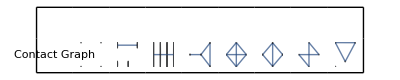

```mathematica
fulllegend =GraphicsGrid[Transpose[Prepend[legend,{"","Contact Graph"}]],Spacings->{Scaled[.5],{Scaled[.01],{},Scaled[.3]}},Frame->True]
```

```mathematica
(*Export["/Users/Valhalla/Documents/UCSB/Campas_Research/Graduate_Research/New_Simulator/Sims with voro/"<>filenamea<>filenameb<>"_plot.pdf",niceplot,Background->None]*)
```

```mathematica
(*Export["/Users/Valhalla/Documents/UCSB/Campas_Research/Graduate_Research/New_Simulator/Sims with voro/"<>filenamea<>filenameb<>"_legend.pdf",fulllegend,Background->None]*)
```

```mathematica
Dimensions[areamat]
```

{1,32,4,4}

```mathematica
areamat[[simnum,1]]//MatrixForm
```

(0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.)

```mathematica
areamat[[1,1]]
```

{{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}}

```mathematica
areas = Table[{areamat[[k,l,1,2]],areamat[[k,l,2,1]],areamat[[k,l,1,3]],areamat[[k,l,3,1]],areamat[[k,l,1,4]],areamat[[k,l,4,1]],areamat[[k,l,2,3]],areamat[[k,l,3,2]],areamat[[k,l,2,4]],areamat[[k,l,4,2]],areamat[[k,l,3,4]],areamat[[k,l,4,3]]},{k,numsims},{l,1,Dimensions[areamat][[2]]}];
```

```mathematica
areas[[1,1]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Dimensions[areas]
```

{1,32,12}

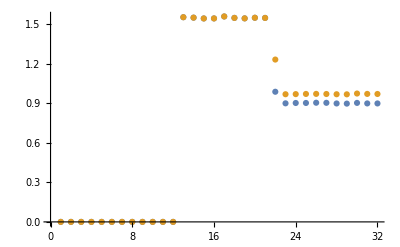

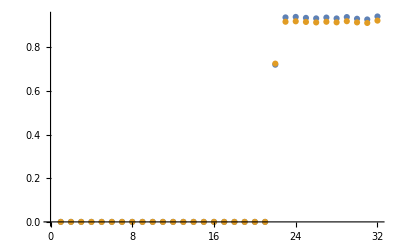

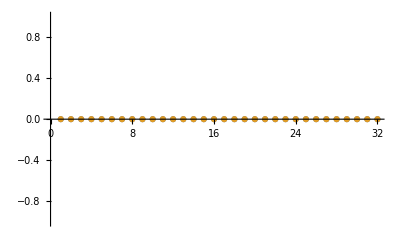

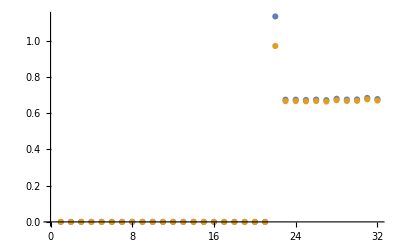

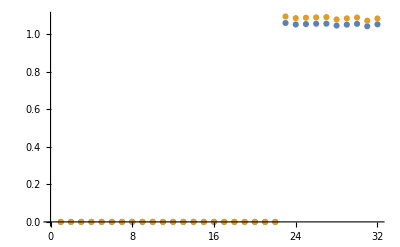

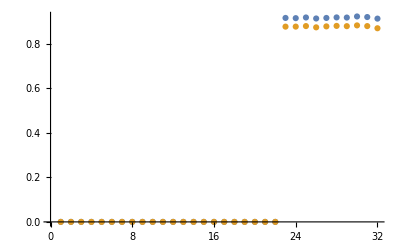

```mathematica
simnum = 1;
ListPlot[{areas[[simnum,All,1]],areas[[simnum,All,2]]}]
ListPlot[{areas[[simnum,All,3]],areas[[simnum,All,4]]}]
ListPlot[{areas[[simnum,All,5]],areas[[simnum,All,6]]}]
ListPlot[{areas[[simnum,All,7]],areas[[simnum,All,8]]}]
ListPlot[{areas[[simnum,All,9]],areas[[simnum,All,10]]}]
ListPlot[{areas[[simnum,All,11]],areas[[simnum,All,12]]}]
```

```mathematica
Dimensions[distdata]
```

{1,32,19}

```mathematica
0.7*(1)*2/(2^(2/3))
```

0.881945

```mathematica
distdata[[1,-1]]
```

{31.,0,1,0.881962,0,2,0.878295,0,3,1.52738,1,2,0.881687,1,3,0.88164,2,3,0.885424}

```mathematica
distpoints = distdata[[All,All,{4,7,10,13,16,19}]];
```

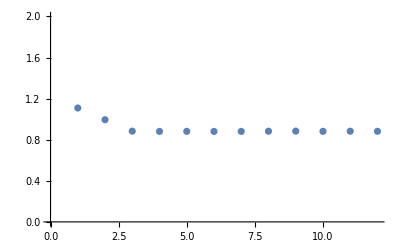

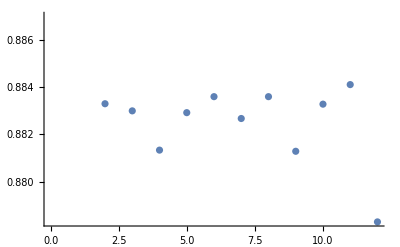

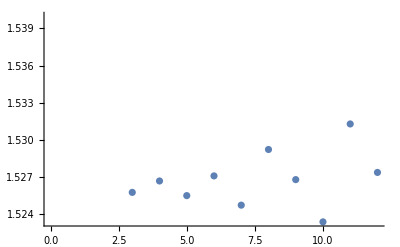

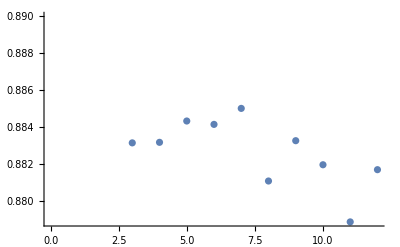

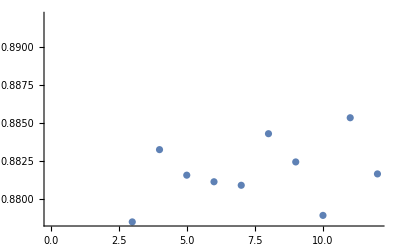

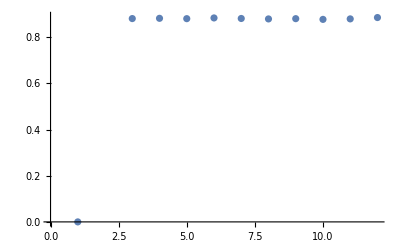

```mathematica
simnum = 1;
ListPlot[distpoints[[simnum,21;;-1,1]],PlotRange->{0,2}]
ListPlot[distpoints[[simnum,21;;-1,2]]]
ListPlot[distpoints[[simnum,21;;-1,3]]]
ListPlot[distpoints[[simnum,21;;-1,4]]]
ListPlot[distpoints[[simnum,21;;-1,5]]]
ListPlot[distpoints[[simnum,21;;-1,6]]]
```

```mathematica
simnum = 1;
(*Manipulate[Grid[{{Graphics3D[{Line[lines1[[x]]]},Boxed->False]},{areamat[[x]]//MatrixForm},{adjgraphs[[x]]}}],{x,1,numfiles,1}]*)
video1 = Table[Show[{ListPointPlot3D[{{point1[[simnum,x,1]],point1[[simnum,x,2]],point1[[simnum,x,3]]},{point2[[simnum,x,1]],point2[[simnum,x,2]],point2[[simnum,x,3]]},{point3[[simnum,x,1]],point3[[simnum,x,2]],point3[[simnum,x,3]]},{point4[[simnum,x,1]],point4[[simnum,x,2]],point4[[simnum,x,3]]}},
PlotRange->{{-2.5,2.5},{-2.5,2.5},{-2.5,2.5}},PlotStyle->PointSize[0.1],BoxRatios->{1,1,1},Boxed->False,Axes->False],Graphics3D[{Opacity[0.3],Ellipsoid[{0,0,0},{sella,sellb,sellc}]}],Graphics3D[{Line[lines1[[simnum,x]]]},Boxed->False]},ViewPoint->Top],{x,1,numfiles,1}];
```

```mathematica
Dimensions[video1]
```

{28}

```mathematica
(*animation1 =ListAnimate[video1,DisplayAllSteps->False,DefaultDuration->5];
fulltablesmall = Table[video1[[i]],{i,1, Dimensions[video1][[1]]}];*)
(*Export["/Users/Valhalla/Documents/UCSB/Campas_Research/Graduate_Research/New_Simulator/Sims with voro/"<>savefile<>"/"<>ar<>"_4square.avi",video1]*)
```

```mathematica
(*Export["/Users/Valhalla/Documents/UCSB/Campas_Research/Graduate_Research/New_Simulator/Sims with voro/2018 Simulator Framework/Testing functions/AR_sims/AR2_V1.84.avi",video1]*)
```

```mathematica
spherepoint = {point1[[-1,-1]],point2[[-1,-1]],point3[[-1,-1]],point4[[-1,-1]]}
```

{{-0.302571,-0.609088,0.229692},{0.534395,-0.33215,0.255225},{-0.126437,0.251309,0.239472},{0.713573,0.531069,0.249156}}

```mathematica
spheres = Table[{Opacity[0.5],Sphere[spherepoint[[i]],1.1/(2^(2/3))]},{i,1,4}];
Show[Graphics3D[Line[lines1[[-1,-1]]]],Graphics3D[spheres](*,ListPointPlot3D[points,PlotStyle->PointSize[0.1],BoxRatios->{1,1,1},Boxed->False,Axes->False]*)]
```

-Graphics3D-

```mathematica
Beep[]
```